```mathematica
k=1
r[x_,y_,z_]:=Sqrt[x^2+y^2+z^2] 
φ[x_,y_,z_]:=ArcTan[y/x] 
θ[x_,y_,z_]:=ArcCos[z/Sqrt[x^2+y^2+z^2] ] 
Vx[x_,y_,z_]:=(k(Cos[θ[x,y,z]]-1))/(r[x,y,z]Sin[θ[x,y,z]])(-Sin[φ[x,y,z]] )
Vy[x_,y_,z_]:= (k(Cos[θ[x,y,z]]-1))/(r[x,y,z]Sin[θ[x,y,z]])Cos[φ[x,y,z]] 
Vz[x_,y_,z_]:=0
p1=VectorPlot3D[{Vx[x,y,z],Vy[x,y,z],Vz[x,y,z]},{x,-1.1,1.1},{y,-1.1,1.1},{z,-1.1,1.1},VectorPoints->20,VectorStyle->"Arrow3D",VectorColorFunction->Function[Hue[Log[#7]/6]], VectorColorFunctionScaling->False, AxesLabel->{"x","y","z"},RegionFunction->Function[{x,y,z},0.95<x^2+y^2+z^2<1.05],VectorScale->{Automatic,Automatic,None}]
p2=Graphics3D[Sphere[{0,0,0},0.95]]
Show[p1,p2]
```

1

-Graphics3D-

-Graphics3D-

-Graphics3D-

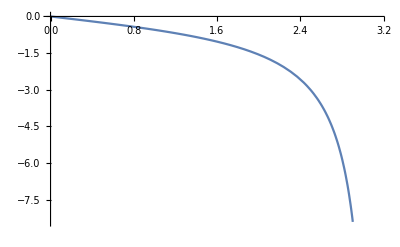

```mathematica
Plot[(Cos[a]-1)/Sin[a],{a,0,π}]
```

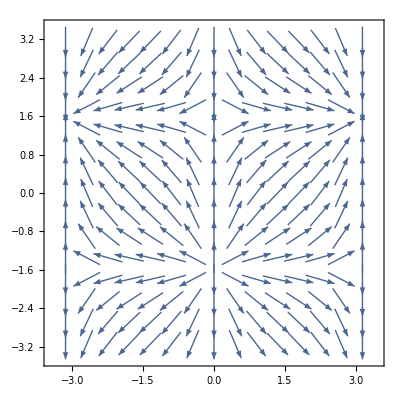
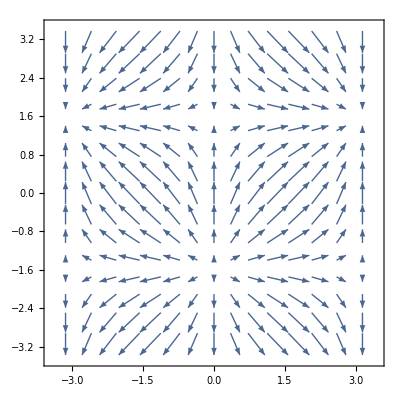

```mathematica
Table[VectorPlot[{Sin[x],Cos[y]},{x,-Pi,Pi},{y,-Pi,Pi},VectorScale->{Automatic,Automatic,f}],{f,{None,Automatic}}]
```